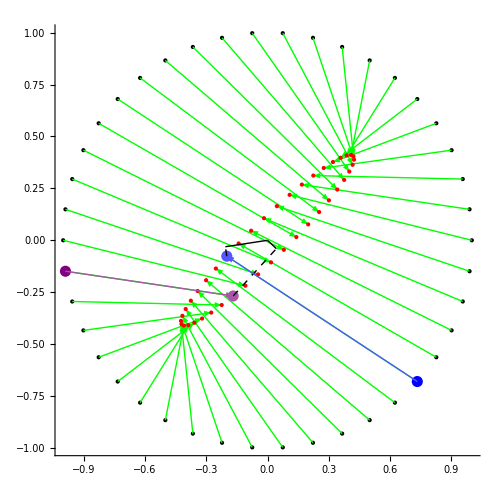

```mathematica
matrix=RandomReal[{0,1},{2,2}];
pts=MeshCoordinates@DiscretizeRegion@Region@Circle[];
evolvedPts=Dot[matrix,#]&/@pts;
pt1=RandomChoice@pts;
evolvedPt1=matrix.pt1;
pt2=RandomChoice@Complement[pts,pt1];
evolvedPt2=matrix.pt2;
Graphics[{
{Point@pts}
,{Green,Arrowheads@0.02,Arrow/@Thread@{pts,evolvedPts}}
,{Red,Point@evolvedPts}
,{
PointSize@0.016,Purple,Point@{pt1}
,Lighter@Purple,Point@{evolvedPt1}
,Arrowheads@0.03,Arrow@{pt1,evolvedPt1}
}
,{
{Dashed,Line@{evolvedPt1,Dot[pt2,evolvedPt1]pt2}}
,Line@{{0,0},Dot[pt2,evolvedPt1]pt2}
}
,{
PointSize@0.016,Blue,Point@{pt2}
,Lighter@Blue,Point@{evolvedPt2}
,Arrowheads@0.03,Arrow@{pt2,evolvedPt2}
}
,{
{Dashed,Line@{evolvedPt2,Dot[pt1,evolvedPt2]pt1}}
,Line@{{0,0},Dot[pt1,evolvedPt2]pt1}
}
},Axes->True,ImageSize->500]
```